```mathematica
gra=Item[#,Background->Lighter[Gray, 0.2]]&;
Grid[({{"xP_11", "xP_12", "xP_13"}, {"xP_21", "xP_22", "xP_23"}, {"xP_31", "xP_32", "xP_33"}})/.{"xP_12"->gra["xP_12"],"xP_32"->gra["xP_32"],"xP_22"->gra["xP_22"]},Frame->All]
```

xP_11 | xP_12 | xP_13
xP_21 | xP_22 | xP_23
xP_31 | xP_32 | xP_33

```mathematica
lr
```

sat::shdw: Symbol sat appears in multiple contexts {life`,Global`}; definitions in context life` may shadow or be shadowed by other definitions.

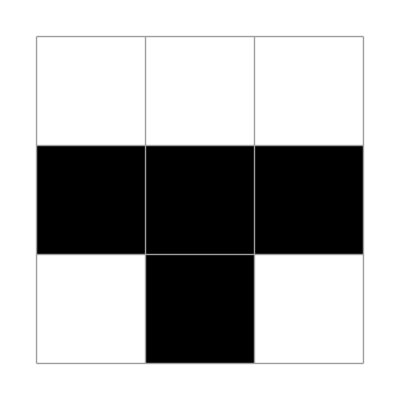
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[varList];
Clear[x11,x12,x13,x21,x22,x23,x31,x32,x33,xE11,xE12,xE13,xE21,xE22,xE23,xE31,xE32,xE33,xN11,xN12,xN13,xN21,xN22,xN23,xN31,xN32,xN33,xNE11,xNE12,xNE13,xNE21,xNE22,xNE23,xNE31,xNE32,xNE33,xNW11,xNW12,xNW13,xNW21,xNW22,xNW23,xNW31,xNW32,xNW33,xS11,xS12,xS13,xS21,xS22,xS23,xS31,xS32,xS33,xSE11,xSE12,xSE13,xSE21,xSE22,xSE23,xSE31,xSE32,xSE33,xSW11,xSW12,xSW13,xSW21,xSW22,xSW23,xSW31,xSW32,xSW33,xW11,xW12,xW13,xW21,xW22,xW23,xW31,xW32,xW33];
Clear[formula,varList,endStateRules];
Clear[out];
Clear[blink190,blinkerRules]
blinkerRules={xP11->False,xP12->True,xP13->False,xP21->False,xP22->True,xP23->False,xP31->False,xP32->True,xP33->False};
blinkerRulesBoundary={
    xSW11->False
,xW11->False
,xNW11->False
,xN11->False
,xNE11->False

,xNW12->False
,xN12->False
,xNE12->False

,xNW13->False
,xN13->False
,xNE13->False
,xE13->False
,xSE13->False


,x23NE->False
,x23E->False
,x23SE->False


,x23NE->False
,x23E->False
,x23SE->False


,x33NE->False
,x33E->False
,x33SE->False
,x33S->False
,x33SW->False


,x32SE->False
,x32S->False
,x32SW->False


,x31NW->False
,x31W->False
,x31SW->False
,x31S->False
,x31SE->False


,x21SW->False
,x21W->False
,x21NW->False

,x11->False
,x33->False
,x31->False
,x13->False
,x12->False


};

endStateRules=blinkerRules~Join~blinkerRulesBoundary;

blink190=And@@({
    the190ForCellIJ[1,1]
,the190ForCellIJ[1,2]
,the190ForCellIJ[1,3]
,the190ForCellIJ[2,1]
,the190ForCellIJ[2,2]
,the190ForCellIJ[2,3]
,the190ForCellIJ[3,1]
,the190ForCellIJ[3,2]
,the190ForCellIJ[3,3]
}/.endStateRules);
varList=
Complement[Join[
    lifeVars[1,1]
,lifeVars[1,2]
,lifeVars[1,3]
,lifeVars[2,1]
,lifeVars[2,2]
,lifeVars[2,3]
,lifeVars[3,1]
,lifeVars[3,2]
,lifeVars[3,3]
]/.endStateRules
,{True,False}];
(out=sat[varList,blink190,10])//Quiet;
outRules=Thread[Rule[Evaluate[varList],out[[3]]]];
(*(({{x11, x12, x13}, {x21, x21, x23}, {x31, x32, x33}})/.Thread[Rule[Evaluate[varList],out[[#]]]]//plt)&/@Range[1000]*)
out;
(plt[({{x11, x12, x13}, {x21, x22, x23}, {x31, x32, x33}})/.Thread[Rule[varList,out[[#]]]]~Join~Boole@endStateRules])&/@Range[Length[out]]

(*(plt[({{xNW, xN, xNE}, {xW, x, xE}, {xSW, xS, xSE}})/.Thread[Rule[varList,out[[#]]]]~Join~Boole@endStateRules])&/@Range[Length[out]]*)
```

```mathematica
lr
```

```mathematica
life44
```

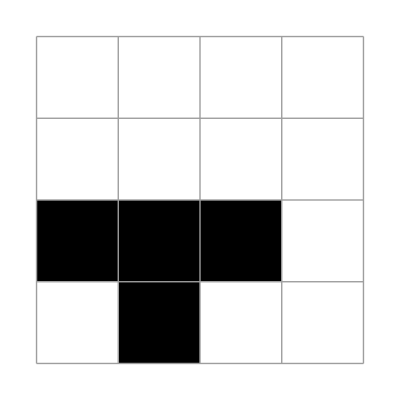
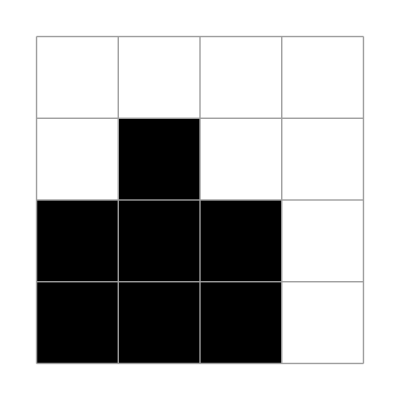
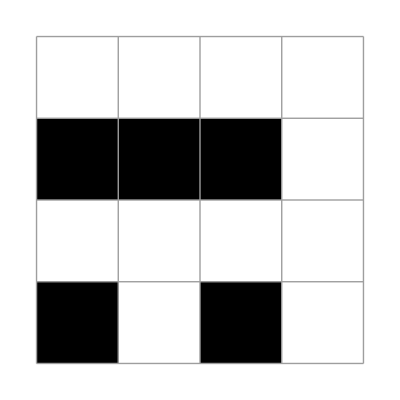
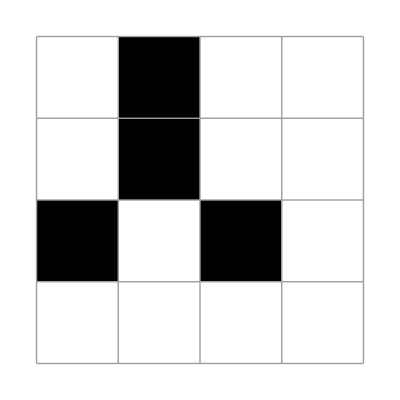

```mathematica
X1=({{0, 0, 0, 0}, {0, 0, 0, 0}, {1, 1, 1, 0}, {0, 1, 0, 0}});
plt/@NestList[updateLife2[{4,4}][ #]&,
X1,3]
```

```mathematica
varList=sat[varList,blink190,1]//First
```

```mathematica
{x11,x12,x13,x21,x22,x23,x31,x32,x33,xE11,xE12,xE13,xE21,xE22,xE23,xE31,xE32,xE33,xN11,xN12,xN13,xN21,xN22,xN23,xN31,xN32,xN33,xNE11,xNE12,xNE13,xNE21,xNE22,xNE23,xNE31,xNE32,xNE33,xNW11,xNW12,xNW13,xNW21,xNW22,xNW23,xNW31,xNW32,xNW33,xS11,xS12,xS13,xS21,xS22,xS23,xS31,xS32,xS33,xSE11,xSE12,xSE13,xSE21,xSE22,xSE23,xSE31,xSE32,xSE33,xSW11,xSW12,xSW13,xSW21,xSW22,xSW23,xSW31,xSW32,xSW33,xW11,xW12,xW13,xW21,xW22,xW23,xW31,xW32,xW33}={0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
varList
```

{x11,x12,x13,x21,x22,x23,x31,x32,x33,xE11,xE12,xE13,xE21,xE22,xE23,xE31,xE32,xE33,xN11,xN12,xN13,xN21,xN22,xN23,xN31,xN32,xN33,xNE11,xNE12,xNE13,xNE21,xNE22,xNE23,xNE31,xNE32,xNE33,xNW11,xNW12,xNW13,xNW21,xNW22,xNW23,xNW31,xNW32,xNW33,xS11,xS12,xS13,xS21,xS22,xS23,xS31,xS32,xS33,xSE11,xSE12,xSE13,xSE21,xSE22,xSE23,xSE31,xSE32,xSE33,xSW11,xSW12,xSW13,xSW21,xSW22,xSW23,xSW31,xSW32,xSW33,xW11,xW12,xW13,xW21,xW22,xW23,xW31,xW32,xW33}

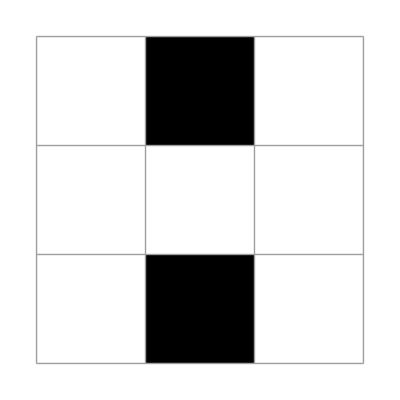

```mathematica
({{x11, x12, x13}, {x21, x21, x23}, {x31, x32, x33}})//plt
```

```mathematica
lifeVars[2,1]
```

{x21,xP21,xNW21,xN21,xNE21,xW21,xE21,xSW21,xS21,xSE21}

```mathematica
varList
```

{0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}